```mathematica
Clear[g];
Clear[a];

(* Exact solve of differential equation *)
sol=DSolve[
{
D[u[x],x]*(u[x]-g*α/(u[x]^2))==-g*f[x]
},
u[x],
x,
Assumptions->{ξ∈Reals,v∈Reals,g∈Reals,α∈Reals}
]
```

{{u[x]→(2 2^(1/3) (C[1]+g f[K[1]]K[1]1x))/((54 g α+√(2916 g^2 α^2+864 (C[1]+g f[K[1]]K[1]1x)^3))^(1/3))-((54 g α+√(2916 g^2 α^2+864 (C[1]+g f[K[1]]K[1]1x)^3))^(1/3))/(3 2^(1/3))},{u[x]→-(2^(1/3) (1+ⅈ √3) (C[1]+g f[K[1]]K[1]1x))/((54 g α+√(2916 g^2 α^2+864 (C[1]+g f[K[1]]K[1]1x)^3))^(1/3))+((1-ⅈ √3) (54 g α+√(2916 g^2 α^2+864 (C[1]+g f[K[1]]K[1]1x)^3))^(1/3))/(6 2^(1/3))},{u[x]→-(2^(1/3) (1-ⅈ √3) (C[1]+g f[K[1]]K[1]1x))/((54 g α+√(2916 g^2 α^2+864 (C[1]+g f[K[1]]K[1]1x)^3))^(1/3))+((1+ⅈ √3) (54 g α+√(2916 g^2 α^2+864 (C[1]+g f[K[1]]K[1]1x)^3))^(1/3))/(6 2^(1/3))}}

```mathematica
(* Arbitrarily look at one of the solutions (one which looks like a real solution) *)
nice=u[x]/.sol[[1]]/.{K[1]->s,α->Subscript[u, 0] Subscript[d, 0]}
```

(2 2^(1/3) (C[1]+g f[s]s1x))/((54 g d_0 u_0+√(2916 g^2 d_0^2 u_0^2+864 (C[1]+g f[s]s1x)^3))^(1/3))-((54 g d_0 u_0+√(2916 g^2 d_0^2 u_0^2+864 (C[1]+g f[s]s1x)^3))^(1/3))/(3 2^(1/3))

```mathematica
profile[x_]:=Exp[-x^2/4^2];
(* Here, f[s] represents dh/dx; integration from 1 to x can be viewed as h(x) up to a constant; but it is multiplied by g. So, what is c_1? I had wanted to call it g*c_2 and define c_2 to be the definite integral of dh/dx from the left hand of the computational domain to x=1... but not sure if completely valid. *)

(* Worth staring at on paper and seeing if it all can be rederived by hand. *)
```

```mathematica
thingy =0+ g*profile[x];
usol=(2 2^(1/3) (thingy))/((54 g Subscript[d, 0] Subscript[u, 0]+√(2916 g^2 Subscript[d, 0]^2 Subscript[u, 0]^2+864 (thingy)^3))^(1/3))-((54 g Subscript[d, 0] Subscript[u, 0]+√(2916 g^2 Subscript[d, 0]^2 Subscript[u, 0]^2+864 (thingy)^3))^(1/3))/(3 2^(1/3));

Dsol=Subscript[u, 0] Subscript[d, 0]/usol;
```

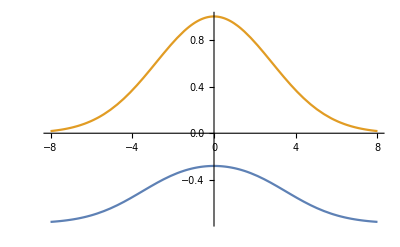

```mathematica
Plot[{
(Dsol+profile[x])/.{Subscript[u, 0]->1,Subscript[d, 0]->3,g->9.8},
profile[x]
},{x,-8,8}]
```

```mathematica
(* clearly not doing something right if Dsol is negative... ? *)
```

```mathematica
(* other solutions look nominally complex but have complex conjugate imag parts *)
(* lin comb for the fun of it *)

guess=FullSimplify[(u[x]/.sol[[2]])+(u[x]/.sol[[3]])]/.{K[1]->s,α->Subscript[u, 0] Subscript[d, 0]}
```

(-2 3^(2/3) C[1]-2 3^(2/3) g f[s]s1x+3^(1/3) (9 g d_0 u_0+1/6 √(2916 g^2 d_0^2 u_0^2+864 (C[1]+g f[s]s1x)^3))^(2/3))/(3 (9 g d_0 u_0+1/6 √(2916 g^2 d_0^2 u_0^2+864 (C[1]+g f[s]s1x)^3))^(1/3))

```mathematica
usol2=(-2 3^(2/3) (thingy)+3^(1/3) (9 g Subscript[d, 0] Subscript[u, 0]+1/6 √(2916 g^2 Subscript[d, 0]^2 Subscript[u, 0]^2+864 (thingy)^3))^(2/3))/(3 (9 g Subscript[d, 0] Subscript[u, 0]+1/6 √(2916 g^2 Subscript[d, 0]^2 Subscript[u, 0]^2+864 (thingy)^3))^(1/3))

Dsol2=Subscript[u, 0] Subscript[d, 0]/usol2;
```

(-2 3^(2/3) ⅇ^(-x^2/16) g+3^(1/3) (9 g d_0 u_0+1/6 √(864 ⅇ^(-(3 x^2)/16) g^3+2916 g^2 d_0^2 u_0^2))^(2/3))/(3 (9 g d_0 u_0+1/6 √(864 ⅇ^(-(3 x^2)/16) g^3+2916 g^2 d_0^2 u_0^2))^(1/3))

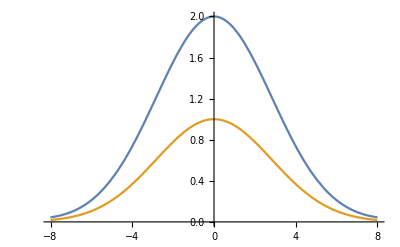

```mathematica
Plot[{
(Dsol2+profile[x])/.{Subscript[u, 0]->1,Subscript[d, 0]->0.01,g->9.8},
profile[x]
},{x,-8,8}]
```

```mathematica
Dsol2
```

(3 d_0 u_0 (9 g d_0 u_0+1/6 √(864 ⅇ^(-(3 x^2)/16) g^3+2916 g^2 d_0^2 u_0^2))^(1/3))/(-2 3^(2/3) ⅇ^(-x^2/16) g+3^(1/3) (9 g d_0 u_0+1/6 √(864 ⅇ^(-(3 x^2)/16) g^3+2916 g^2 d_0^2 u_0^2))^(2/3))